# Integration Approximation Error

### Overview

When numerical approximation techniques are used for integration, some amount of error is unavoidable.  
In this lab we will explore:
1. the case where we can compare an approximation to an exact value, 
2. the case where we can only bound the error, because an exact result is unknown.

### Instructions

1. Read through the notebook top to bottom, executing cells as you go.
2. Complete the quiz in Canvas.

## Comparison to Actual Error

We will first explore the situation in which an antiderivative in terms of elementary functions cannot be found.   Execute the following cell to try and evaluate exactly ∫_0^1 ⅇ^(-x^2)ⅆx.

```mathematica
Integrate[E^(-x^2),{x,0,1}]
```

1/2 √π Erf[1]

If you needed to take the result of this integral and use it in a calculation, that would be difficult to do since the result is a function and not a number. You can read more about the “error function” here:  http://mathworld.wolfram.com/Erf.html

This is a situation where we might wish to use an integration approximation algorithm such as the Midpoint Rule to produce a numerical solution.  The code below uses the Midpoint Rule to approximate ∫_a^b f(x)ⅆx=∫_0^1 ⅇ^(-x^2)ⅆx using n subintervals.

```mathematica
f[x_]:=E^(-x^2);
g[n_]:=Module[{},a=0;
b=1;
Δx=(b-a)/n;
x[i_]=a+i Δx;
xbar[i_]=1/2(x[i-1]+x[i]);
.746824-(Δx(Sum[f[xbar[i]],{i,1,n}]))//N]
```

```mathematica
g[#]&/@{3,9,27}
```

{-0.00342835,-0.000378882,-0.0000421892}

```mathematica
g[9]
```

-0.000378882

```mathematica
g[27]
```

-0.0000421892

```mathematica
r1/r2
```

1.00408

```mathematica
g[#]&/@{3,9,27}
```

{-0.00342835,-0.000378882,-0.0000421892}

```mathematica
g[3]
```

-0.00342835

```mathematica
Table[g[3^i],{i,1,3}]
```

{-0.148015,-0.204993,-0.240906}

```mathematica
g[2]
```

0.778801

```mathematica
Evaluate[g[9]]/Evaluate[g[27]]
```

8.98055

```mathematica
g[27]
```

-0.0000421892

```mathematica
g[9]/g[27]
```

8.98055

```mathematica
Table[i,{i,1,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
(g[3^#]/g[3^(#+1)])&/@Table[i,{i,1,3}]
```

{9.04859,8.98055,8.77952}

```mathematica
g[9]/g[27]
```

8.98055

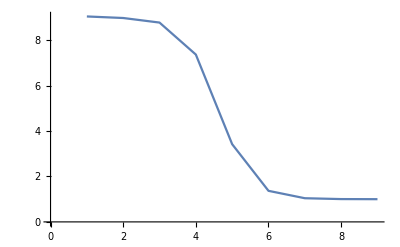

```mathematica
ListLinePlot[(g[3^#]/g[3^(#+1)])&/@Table[i,{i,1,9}]]
```

```mathematica
r1/r2
```

1.00408

```mathematica
r2/r3
```

1.00045

If you had an exact value for the integral that you approximated via the Midpoint Rule, you could calculate the error in your estimate as Error = Actual - Approximation.  You will see in the quiz associated with this lab that varying n changes the size of the error by a predictable amount.

## Determining an Error Bound

What if we don’t have an actual value to compare our approximation to?  In that case, the best we can do is to bound the error.  That means we can quantify the maximum possible deviation from the actual value.  For the Midpoint Rule, the error bound is given by the right side of the following inequality:

|E_M|≤(K(b-a))^3/(24 n^2), where |f''(x)|≤K for a≤x≤b.

You should try to bound the error as tightly as possible for a given n.  To accomplish this, you need to choose the smallest K that still satisfies |f''(x)|≤K for a≤x≤b (i.e. choose K to be the maximum value of |f''(x)| over the interval).  

We’ll look at two approaches for finding this K:  an analytical method and a graphical method.

### Analytical Approach to Determining K

This technique will use the commands FindRoot and ReplaceAll, which you should have learned in Calc 1.  In case you need it, a review of these commands is provided at the bottom of this notebook.

We wish to bound the error in the approximation given by the Midpoint Rule for ∫_a^b f(x)ⅆx=∫_0^(π/2) 2cos(x)+sin(2x) ⅆx.

We need the absolute maximum and minimum values of f''(x) on the closed interval [a, b].  We’ll compare the absolute values of these extrema and choose the largest (or a number slightly larger) for K.  

We’ll follow the process you learned in Calc 1 for finding maximum and minimum values.  

First we need the critical numbers of f'' in (a, b).  These are the x values between a and b for which the DERIVATIVE of f'' (that is, f''') is zero or does not exist.  We start by taking the third derivative of f :

```mathematica
f[x_]:=Cos[x^2]+Sin[3x];
f'''[x]
```

-27 Cos[3 x]-12 x Cos[x^2]+8 x^3 Sin[x^2]

The resulting function, f''', is defined for all values of x, so we just need to see if it ever equals zero on the interval (0, π/2).  We can check this by plotting f''' on that interval:

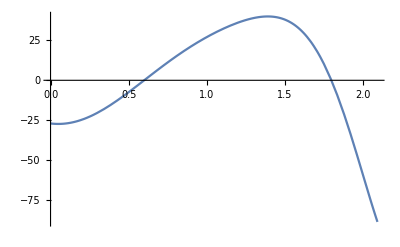

```mathematica
Plot[f'''[x],{x,0,(2Pi)/3}]
```

It is clear from the graph that there’s a critical number near 0.7.  We’ll use the FindRoot command to find a more accurate estimate of this critical number.  For ease of reference later on, let’s name this root x1 by using the ReplaceAll command, /. :

```mathematica
x1=x/.FindRoot[f'''[x]==0,{x,0.7}]
```

0.599938

```mathematica
x2=x/.FindRoot[f'''[x]==0,{x,1.8}]
```

1.79903

Now we want to find f''(x) at the critical number x1 and at the endpoints of the interval, a=0 and b=π/2 :

```mathematica
f''[x1]
f''[x2]
f''[0]
f''[(2Pi)/3]//N
```

-10.8169

20.0488

0

7.51224

Comparing these 3 numbers, we conclude that the absolute maximum of  f''(x) on [a, b] is 0, while the absolute minimum is approximately -5.47163 (remember that Mathematica is only showing us 5 decimal places of accuracy).  We want |f''(x)|≤K for a≤x≤b, so we choose K so that it is slightly larger than 5.47163.  Setting K=5.5 would be a good choice here.

### Graphical Approach to Determining K

A second, though potentially less precise, way to determine K is to look at the graph of the second derivative of the function we would like to integrate, and to identify the maximum value of |f''(x)|from the graph.  Suppose again that we are interested in using the Midpoint Rule to approximate ∫_0^(π/2) 2cos(x)+sin(2x) ⅆx.  First I’ll compute  f''(x) :

```mathematica
f[x_]:=2Cos[x]+Sin[2x];
f''[x]
```

-2 Cos[x]-4 Sin[2 x]

Now I’ll plot this second derivative over the interval of integration, 0 to π/2 :

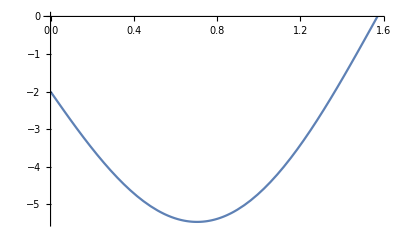

```mathematica
Plot[f''[x],{x,0,Pi/2}]
```

Since |f''(x)|≤ 6 along the entire interval of interest, this would be an acceptable choice for K.  Note that the analytical approach let me confidently choose a smaller value for K, resulting in a tighter error bound.

### Using K to Compute the Error Bound

The code below computes the error bound for the Midpoint Rule, |E_M|≤(K(b-a))^3/(24 n^2).  Use the slider to explore how changing n affects the maximum error to be expected.  Click on the “+“ inside the square to see the value of n that gives a particular bound.

```mathematica
a=0;
b=Pi/2;
K=17;
MidpointErrorBound=Manipulate[(K(b-a)^3)/(24 n^2)//N,{n,1,100,1}]
```

I can see that if I want the error in my approximation to be less than 0.0008, I have to use at least n = 34 subintervals.

## Review from Calc 1: Finding Roots

### Roots

Given an equation f(x), the roots of the equation are the solutions to f(x)=0. For example, if f(x)=2 x^2+6x-20 , then the roots of f(x) are the solutions to 2 x^2+6x-20=0 . One way to find these roots is to use the FindRoot command.

### FindRoot

The FindRoot command does just what it says, it finds a root of a function. Notice I said root and not roots. FindRoot takes the function as its first argument, but as its second argument it takes the variable and a starting point to search from. For example:

```mathematica
FindRoot[2 x^2+6x-20,{x,1}]
```

{x→2.}

Note that we only found the x=2 root. If we want to find the other root we would have to start our search somewhere else.

```mathematica
FindRoot[2 x^2+6x-20,{x,-20}]
```

{x→-5.}

### Keeping your Results

To keep the results of the FindRoot command, you’ll need to use the ReplaceAll command, which looks like this:    /.
The reason is that the FindRoot command outputs a replacement rule (for example, {x→5} ).  To keep the results of FindRoot for later use we need to replace the variable with the replacement rule and then store that value to a new variable. See the example below:

```mathematica
h[x_]=4Cos[3x];
a=x/.FindRoot[h[x]==0,{x,.5}]
f[a]
```

0.523599

-6.43249×10^-16